# MITOCW 8.05-2013

## P7, PSET 4

#### In this section, we will perform the Gram-Schmidt algorithm and approximate Sine and Cosine in U space

7b) This is the constructor for the Non-orthogonal Basis of just the first num powers of x (for our cause, n=6) in U:

```mathematica
UnorthogonalBasis={};
num=6;
For[i=0,i<num,i++,AppendTo[UnorthogonalBasis,x^i]];
Print[UnorthogonalBasis]
```

{1,x,x^2,x^3,x^4,x^5}

Now we orthonormalize our basis in U:

```mathematica
DotBasis=Orthogonalize[UnorthogonalBasis,Integrate[#1 #2,{x,-Pi,Pi}]&]
```

{1/(√(2 π)),(√(3/2) x)/π^(3/2),(3 √(5/2) (-π^2/3+x^2))/(2 π^(5/2)),(5 √(7/2) (-(3 π^2 x)/5+x^3))/(2 π^(7/2)),(105 (-π^4/5+x^4-6/7 π^2 (-π^2/3+x^2)))/(8 √2 π^(9/2)),(63 √(11/2) (-(3 π^4 x)/7+x^5-10/9 π^2 (-(3 π^2 x)/5+x^3)))/(8 π^(11/2))}

7c) ext we find the coefficients of these polynomials for Sin(x) and Cosine(x) in U:

```mathematica
CoefficientsSine=Integrate[Sin[x]*DotBasis,{x,-Pi,Pi}];CoefficientsCosine=Integrate[Cos[x]*DotBasis,{x,-Pi,Pi}];Print[CoefficientsSine];Print[CoefficientsCosine];
```

{0,√(6/π),0,(√14 (-15+π^2))/π^(5/2),0,(√22 (945-105 π^2+π^4))/π^(9/2)}

{0,0,-(3 √10)/π^(3/2),0,-(15 √2 (-21+2 π^2))/π^(7/2),0}

Now, we find the polynomial expansion for sine and cosine in U, These are coefficients in terms of π:

```mathematica
SinePoly=0;For[i=1,i<num+1,i++,SinePoly=MapThread[Times,{DotBasis,CoefficientsSine}][[i]]+SinePoly];SinePoly=Collect[SinePoly,x];
CosinePoly=0;For[i=1,i<num+1,i++,CosinePoly=MapThread[Times,{DotBasis,CoefficientsCosine}][[i]]+CosinePoly];CosinePoly=Collect[CosinePoly,x];
Print[SinePoly]; Print[CosinePoly]
```

(3/π^2-(21 (-15+π^2))/(2 π^4)+(165 (945-105 π^2+π^4))/(8 π^6)) x+((35 (-15+π^2))/(2 π^6)-(385 (945-105 π^2+π^4))/(4 π^8)) x^3+(693 (945-105 π^2+π^4) x^5)/(8 π^10)

15/(2 π^2)-(135 (-21+2 π^2))/(8 π^4)+(-45/(2 π^4)+(675 (-21+2 π^2))/(4 π^6)) x^2-(1575 (-21+2 π^2) x^4)/(8 π^8)

Now, we find the polynomial expansion for sine and cosine in U, These are numerical coefficients :

```mathematica
SinePoly=0;For[i=1,i<num+1,i++,SinePoly=N[MapThread[Times,{DotBasis,CoefficientsSine}]][[i]]+SinePoly];SinePoly=Collect[SinePoly,x];
CosinePoly=0;For[i=1,i<num+1,i++,CosinePoly=N[MapThread[Times,{DotBasis,CoefficientsCosine}]][[i]]+CosinePoly];CosinePoly=Collect[CosinePoly,x];
Print[SinePoly]; Print[CosinePoly]
```

0.+0.987862 x-0.155271 x^3+0.00564312 x^5

0.978326-0.452288 x^2+0.0261598 x^4

Next, we find the Taylor polynomial:(As you see, there is a good agreement in the first few terms, try increasing num, to get better agreement for a larger number of terms)

```mathematica
SineTaylor=Collect[N[Series[Sin[x],{x,0,num}]],x];CosineTaylor=Collect[N[Series[Cos[x],{x,0,num}]],x];Print[SineTaylor];Print[CosineTaylor]
```

1. x-0.166667 x^3+0.00833333 x^5

1.-0.5 x^2+0.0416667 x^4-0.00138889 x^6

7d) These are the plots, the approximation in U is better than the Taylor approximation.

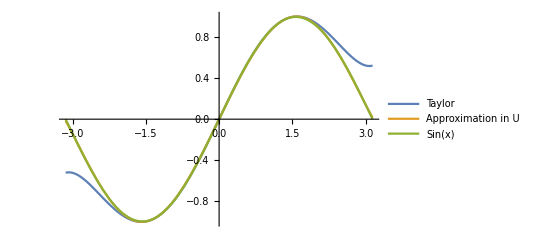

```mathematica
Plot[{SineTaylor,SinePoly,Sin[x]},{x,-Pi,Pi},PlotLegends->{"Taylor","Approximation in U","Sin(x)"}]
```

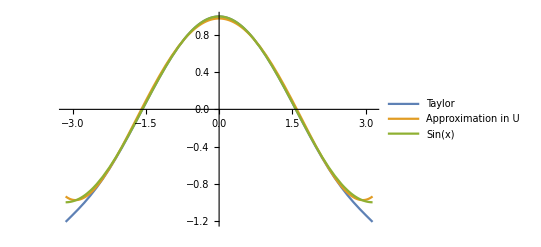

```mathematica
Plot[{CosineTaylor,CosinePoly,Cos[x]},{x,-Pi,Pi},PlotLegends->{"Taylor","Approximation in U","Sin(x)"}]
```